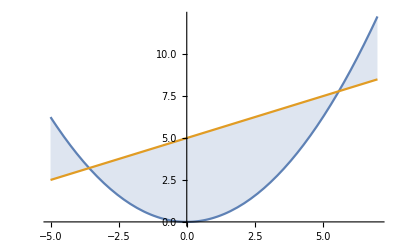

```mathematica
f[y_]=y^2/4;
g[y_]=(y+10)/2;
Plot[{f[y],g[y]},{y,-5,7},Filling->{1->{2}}]
```

```mathematica
NSolve[f[y]==g[y]]
```

{{y→-3.58258},{y→5.58258}}

```mathematica
Integrate[-f[y]+g[y],{y,-3.58258,5.58258}]
```

32.078